# Improved Ambient Occlusion

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0 is the radiance value perceived from the (distant) environment and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).

We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=(ρ(x'))/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ (ρ(x'))/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that, assuming a constant reflectance everywhere so (ρ(x'))/π=(ρ(x))/π=ρ/π, we can compute each bounce of the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations since:
	E_(n+1)(x)=ρ/π∫_Ω^□ E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

## Fitting Experimental Data

After writing the program that computes the AO and the multiple indirect bounces from a height map, we collect the bounced illuminance values into histograms where the bin indices are given by the AO values: this bascially computes the average indirect illuminance perceived by a point given its AO value (AO value is in [0,2π] but we rescaled it to [0,1] for energy conservation purposes).
We do that for multiple bounces to try and find a pattern in the shape and amplitude of the curves...

To generate the curves shown below, we used the WallHeight.png as a height map, and its corresponding WallNormal.png as a normal map.
We also chose a height value of 10 cm for a total wall length of 1 meter, 1024 rays at 179° cone aperture.
It gave some nice curves without the annoying artefacts found at the extremas that can be found with other maps.

```mathematica
ClearAll["Global`*"]
```

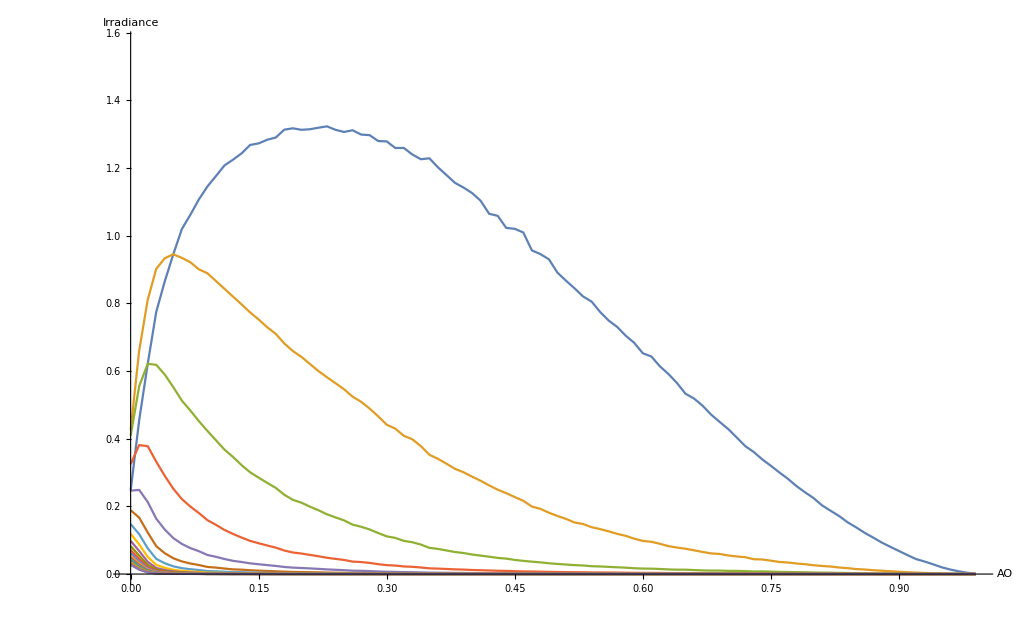

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize =samplesCount= 100;
bouncesCount = 20;
rawArray=Table[ BinaryReadList["Results/WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListLinePlot[bounces,PlotRange->{0,π/2},AxesLabel->{"AO","Irradiance"}]
```

Here we show the influence on the maximum height encoded by the height map on the resulting histogram curves: we see that apart from a slight compression to the left on bounce indices > 1, they are basically identical.
We notice a small discrepancy in the 5 cm curve and assume it will get worse when the height amplitudes continue to decrease, eventually becoming totally flat so no bounce can occur at all.
We can imagine the smae phenomenon occurs when the height map amplitudes become very large so no direct light can even reach the bottom of the surface.
Anyway, we will focus on the “normal regime” by assuming a height amplitude equal to 1/10 the size of the height map.
The height map we used is noisy enough (a brick wall texture with many details) to be considered a general  case from which all other cases derive.

```mathematica
(*bounces5cm = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];*)
(*bounces15cm = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];*)
(*bounces25cm = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];*)
(*Manipulate[Show[
ListLinePlot[bounces[[bounceIndex]],PlotRange->{0,π/2}],
ListLinePlot[bounces5cm[[bounceIndex]],PlotRange->Full,PlotStyle->Red],
ListLinePlot[bounces15cm[[bounceIndex]],PlotRange->Full,PlotStyle->Green],
ListLinePlot[bounces25cm[[bounceIndex]],PlotRange->Full,PlotStyle->Blue]
],{bounceIndex,1,bouncesCount,1}]*)
```

These were the original curves where I made the mistake of using initial direct illuminance E0 instead of AO to drive the histogram bins storage:

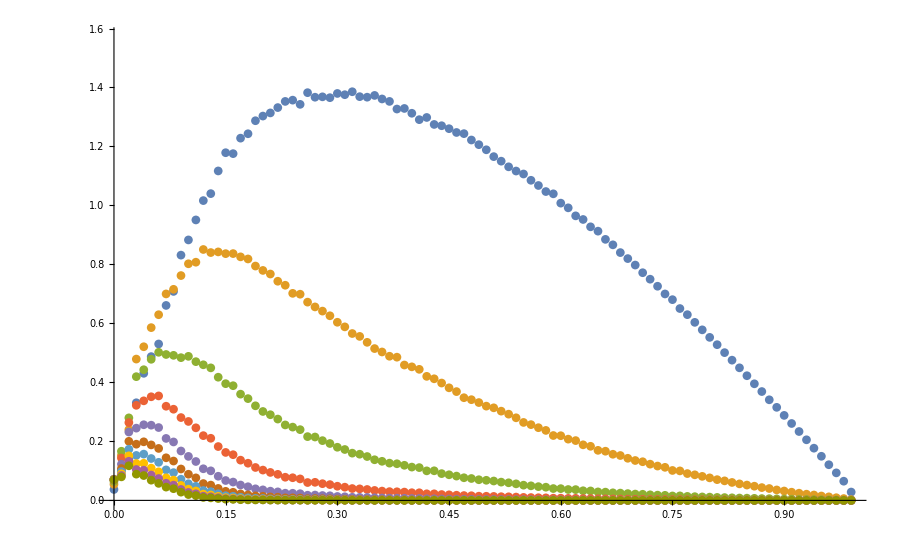

-Graphics-

## Fitting the Difference between Actual Direct Irradiance and AO Simplification

Showing the irradiance received directly, without any bounce, as a function of AO:

BinaryReadList::nffil: File not found during BinaryReadList["WallHeight0.float", "Real32"].

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

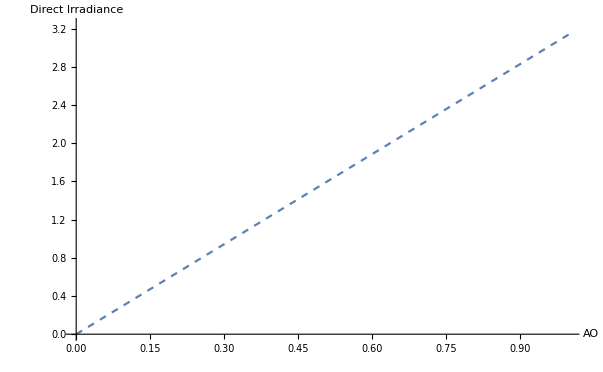

```mathematica
rawArray0=BinaryReadList["Results/WallHeight0.float", "Real32"];
taE0 = Table[{(i-1)/(tableSize-1),rawArray0[[i]]},{i,1,tableSize}];
Show[ListLinePlot[taE0,PlotRange->{{0,1},{0,π+0.1}},AxesLabel->{"AO","Direct Irradiance"}],Plot[π*x,{x,0,1},PlotStyle->Dashed]]
```

```mathematica
flatE0 = Table[{(i-1)/(tableSize-1),rawArray0[[i]]-(i-1)/(tableSize-1)*(rawArray0[[tableSize]]-rawArray0[[1]]) - rawArray0[[1]]},{i,1,tableSize}];
ListLinePlot[flatE0,PlotRange->{0,0.5},AxesLabel->{"AO","Direct Irradiance Delta"}]
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 100 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[a,b,c,x,modelEO,fitEO];
modelE0=a * x^b*(1-x)^c;
modelE0=a+1.5 * x^1*(1-x)^0.75;
fitE0=FindFit[flatE0,{modelE0,b >0,c>0},{a,{b,1},c},{x}]
Show[
ListLinePlot[flatE0,PlotRange->Full],
Plot[modelE0/.fitE0,{x,0,1}]
]
```

FindFit::nrnum: The function value 1/2\ (2.  + (1.01504  + $Failed ⟦ 1 ⟧ - $Failed ⟦ 2 ⟧ + 1/99\ (-Part[« 2 »] + $Failed ⟦ 100 ⟧))^2 + (1.02984  + $Failed ⟦ 1 ⟧ - $Failed ⟦ 3 ⟧ + 2/99\ (-Part[« 2 »] + $Failed ⟦ 100 ⟧))^2 + « 45 » + (1.44223  + $Failed ⟦ 1 ⟧ - $Failed ⟦ 49 ⟧ + 16/33\ (-Part[« 2 »] + $Failed ⟦ 100 ⟧))^2 + (1.44479  + $Failed ⟦ 1 ⟧ - $Failed ⟦ 50 ⟧ + 49/99\ (-Part[« 2 »] + $Failed ⟦ 100 ⟧))^2 + « 49 ») is not a real number at {a, b, c} = {1., 1., 1.}.

FindFit[{{0,0},{1/99,-$Failed⟦1⟧+$Failed⟦2⟧+1/99 ($Failed⟦1⟧-$Failed⟦100⟧)},{2/99,-$Failed⟦1⟧+$Failed⟦3⟧-2/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{1/33,-$Failed⟦1⟧+$Failed⟦4⟧+1/33 ($Failed⟦1⟧-$Failed⟦100⟧)},{4/99,-$Failed⟦1⟧+$Failed⟦5⟧-4/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{5/99,-$Failed⟦1⟧+$Failed⟦6⟧-5/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{2/33,-$Failed⟦1⟧+$Failed⟦7⟧-2/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{7/99,-$Failed⟦1⟧+$Failed⟦8⟧-7/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{8/99,-$Failed⟦1⟧+$Failed⟦9⟧-8/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{1/11,-$Failed⟦1⟧+$Failed⟦10⟧+1/11 ($Failed⟦1⟧-$Failed⟦100⟧)},{10/99,-$Failed⟦1⟧+$Failed⟦11⟧-10/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{1/9,-$Failed⟦1⟧+$Failed⟦12⟧+1/9 ($Failed⟦1⟧-$Failed⟦100⟧)},{4/33,-$Failed⟦1⟧+$Failed⟦13⟧-4/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{13/99,-$Failed⟦1⟧+$Failed⟦14⟧-13/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{14/99,-$Failed⟦1⟧+$Failed⟦15⟧-14/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{5/33,-$Failed⟦1⟧+$Failed⟦16⟧-5/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{16/99,-$Failed⟦1⟧+$Failed⟦17⟧-16/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{17/99,-$Failed⟦1⟧+$Failed⟦18⟧-17/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{2/11,-$Failed⟦1⟧+$Failed⟦19⟧-2/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{19/99,-$Failed⟦1⟧+$Failed⟦20⟧-19/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{20/99,-$Failed⟦1⟧+$Failed⟦21⟧-20/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{7/33,-$Failed⟦1⟧+$Failed⟦22⟧-7/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{2/9,-$Failed⟦1⟧+$Failed⟦23⟧-2/9 (-$Failed⟦1⟧+$Failed⟦100⟧)},{23/99,-$Failed⟦1⟧+$Failed⟦24⟧-23/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{8/33,-$Failed⟦1⟧+$Failed⟦25⟧-8/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{25/99,-$Failed⟦1⟧+$Failed⟦26⟧-25/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{26/99,-$Failed⟦1⟧+$Failed⟦27⟧-26/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{3/11,-$Failed⟦1⟧+$Failed⟦28⟧-3/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{28/99,-$Failed⟦1⟧+$Failed⟦29⟧-28/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{29/99,-$Failed⟦1⟧+$Failed⟦30⟧-29/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{10/33,-$Failed⟦1⟧+$Failed⟦31⟧-10/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{31/99,-$Failed⟦1⟧+$Failed⟦32⟧-31/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{32/99,-$Failed⟦1⟧+$Failed⟦33⟧-32/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{1/3,-$Failed⟦1⟧+$Failed⟦34⟧+1/3 ($Failed⟦1⟧-$Failed⟦100⟧)},{34/99,-$Failed⟦1⟧+$Failed⟦35⟧-34/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{35/99,-$Failed⟦1⟧+$Failed⟦36⟧-35/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{4/11,-$Failed⟦1⟧+$Failed⟦37⟧-4/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{37/99,-$Failed⟦1⟧+$Failed⟦38⟧-37/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{38/99,-$Failed⟦1⟧+$Failed⟦39⟧-38/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{13/33,-$Failed⟦1⟧+$Failed⟦40⟧-13/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{40/99,-$Failed⟦1⟧+$Failed⟦41⟧-40/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{41/99,-$Failed⟦1⟧+$Failed⟦42⟧-41/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{14/33,-$Failed⟦1⟧+$Failed⟦43⟧-14/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{43/99,-$Failed⟦1⟧+$Failed⟦44⟧-43/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{4/9,-$Failed⟦1⟧+$Failed⟦45⟧-4/9 (-$Failed⟦1⟧+$Failed⟦100⟧)},{5/11,-$Failed⟦1⟧+$Failed⟦46⟧-5/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{46/99,-$Failed⟦1⟧+$Failed⟦47⟧-46/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{47/99,-$Failed⟦1⟧+$Failed⟦48⟧-47/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{16/33,-$Failed⟦1⟧+$Failed⟦49⟧-16/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{49/99,-$Failed⟦1⟧+$Failed⟦50⟧-49/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{50/99,-$Failed⟦1⟧+$Failed⟦51⟧-50/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{17/33,-$Failed⟦1⟧+$Failed⟦52⟧-17/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{52/99,-$Failed⟦1⟧+$Failed⟦53⟧-52/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{53/99,-$Failed⟦1⟧+$Failed⟦54⟧-53/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{6/11,-$Failed⟦1⟧+$Failed⟦55⟧-6/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{5/9,-$Failed⟦1⟧+$Failed⟦56⟧-5/9 (-$Failed⟦1⟧+$Failed⟦100⟧)},{56/99,-$Failed⟦1⟧+$Failed⟦57⟧-56/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{19/33,-$Failed⟦1⟧+$Failed⟦58⟧-19/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{58/99,-$Failed⟦1⟧+$Failed⟦59⟧-58/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{59/99,-$Failed⟦1⟧+$Failed⟦60⟧-59/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{20/33,-$Failed⟦1⟧+$Failed⟦61⟧-20/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{61/99,-$Failed⟦1⟧+$Failed⟦62⟧-61/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{62/99,-$Failed⟦1⟧+$Failed⟦63⟧-62/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{7/11,-$Failed⟦1⟧+$Failed⟦64⟧-7/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{64/99,-$Failed⟦1⟧+$Failed⟦65⟧-64/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{65/99,-$Failed⟦1⟧+$Failed⟦66⟧-65/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{2/3,-$Failed⟦1⟧+$Failed⟦67⟧-2/3 (-$Failed⟦1⟧+$Failed⟦100⟧)},{67/99,-$Failed⟦1⟧+$Failed⟦68⟧-67/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{68/99,-$Failed⟦1⟧+$Failed⟦69⟧-68/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{23/33,-$Failed⟦1⟧+$Failed⟦70⟧-23/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{70/99,-$Failed⟦1⟧+$Failed⟦71⟧-70/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{71/99,-$Failed⟦1⟧+$Failed⟦72⟧-71/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{8/11,-$Failed⟦1⟧+$Failed⟦73⟧-8/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{73/99,-$Failed⟦1⟧+$Failed⟦74⟧-73/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{74/99,-$Failed⟦1⟧+$Failed⟦75⟧-74/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{25/33,-$Failed⟦1⟧+$Failed⟦76⟧-25/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{76/99,-$Failed⟦1⟧+$Failed⟦77⟧-76/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{7/9,-$Failed⟦1⟧+$Failed⟦78⟧-7/9 (-$Failed⟦1⟧+$Failed⟦100⟧)},{26/33,-$Failed⟦1⟧+$Failed⟦79⟧-26/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{79/99,-$Failed⟦1⟧+$Failed⟦80⟧-79/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{80/99,-$Failed⟦1⟧+$Failed⟦81⟧-80/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{9/11,-$Failed⟦1⟧+$Failed⟦82⟧-9/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{82/99,-$Failed⟦1⟧+$Failed⟦83⟧-82/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{83/99,-$Failed⟦1⟧+$Failed⟦84⟧-83/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{28/33,-$Failed⟦1⟧+$Failed⟦85⟧-28/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{85/99,-$Failed⟦1⟧+$Failed⟦86⟧-85/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{86/99,-$Failed⟦1⟧+$Failed⟦87⟧-86/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{29/33,-$Failed⟦1⟧+$Failed⟦88⟧-29/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{8/9,-$Failed⟦1⟧+$Failed⟦89⟧-8/9 (-$Failed⟦1⟧+$Failed⟦100⟧)},{89/99,-$Failed⟦1⟧+$Failed⟦90⟧-89/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{10/11,-$Failed⟦1⟧+$Failed⟦91⟧-10/11 (-$Failed⟦1⟧+$Failed⟦100⟧)},{91/99,-$Failed⟦1⟧+$Failed⟦92⟧-91/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{92/99,-$Failed⟦1⟧+$Failed⟦93⟧-92/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{31/33,-$Failed⟦1⟧+$Failed⟦94⟧-31/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{94/99,-$Failed⟦1⟧+$Failed⟦95⟧-94/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{95/99,-$Failed⟦1⟧+$Failed⟦96⟧-95/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{32/33,-$Failed⟦1⟧+$Failed⟦97⟧-32/33 (-$Failed⟦1⟧+$Failed⟦100⟧)},{97/99,-$Failed⟦1⟧+$Failed⟦98⟧-97/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{98/99,-$Failed⟦1⟧+$Failed⟦99⟧-98/99 (-$Failed⟦1⟧+$Failed⟦100⟧)},{1,0}},{a+1.5 (1-x)^0.75 x,b>0,c>0},{a,{b,1},c},{x}]

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0000204286 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{0, 0}, {1/99, -$Failed ⟦ 1 ⟧ + $Failed ⟦ 2 ⟧ + 1/99\ (Part[« 2 »] + Times[« 2 »])}, {2/99, -$Failed ⟦ 1 ⟧ + $Failed ⟦ 3 ⟧ - 2/99\ (Times[« 2 »] + Part[« 2 »])}, {1/33, -$Failed ⟦ 1 ⟧ + $Failed ⟦ 4 ⟧ + 1/33\ (Part[« 2 »] + Times[« 2 »])}, {4/99, -$Failed ⟦ 1 ⟧ + $Failed ⟦ 5 ⟧ - 4/99\ (Times[« 2 »] + Part[« 2 »])}, « 42 », {47/99, -$Failed ⟦ 1 ⟧ + $Failed ⟦ 48 ⟧ - 47/99\ (Times[« 2 »] + Part[« 2 »])}, {16/33, -$Failed ⟦ 1 ⟧ + $Failed ⟦ 49 ⟧ - 16/33\ (Times[« 2 »] + Part[« 2 »])}, {49/99, -$Failed ⟦ 1 ⟧ + $Failed ⟦ 50 ⟧ - 49/99\ (Times[« 2 »] + Part[« 2 »])}, « 50 »}, {« 1 »}, « 1 », {« 24 »}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

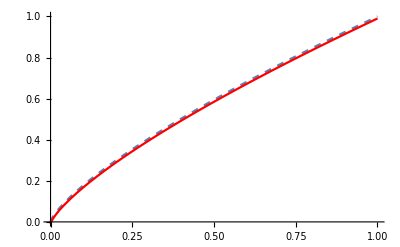

```mathematica
Show[
Plot[x^0.75,{x,0,1},PlotStyle->Dashed],
Plot[x/(√(√x))-0.01,{x,0,1},PlotStyle->Red]
]
```

π (x+0.5 (1-x)^(3/4) x)

π (1+0.5 (1-x)^(3/4)) x

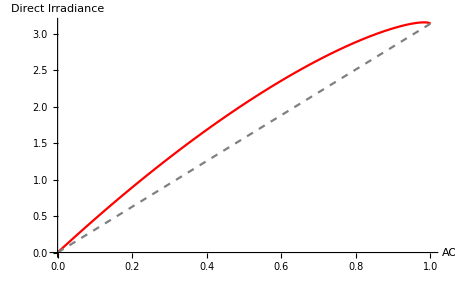

```mathematica
Clear[F,G,F0,E0]
E0[x_]=π*(x+0.5*x*(1-x)/(√(√(1-x))))
E0[x_]=π*(x*(1+0.5*(1-x)/(√(√(1-x)))))
Show[
ListLinePlot[taE0,PlotRange->{0,0.01+π},PlotStyle->{Dashed,Thickness->0.01},AxesLabel->{"AO","Direct Irradiance"}],
Plot[E0[x],{x,0,1},PlotStyle->Red],
Plot[π*x,{x,0,1},PlotStyle->{Dashed,Gray}]
]
```

## Summing the Curves

These curves represent the initial unit luminance reflected N times.

```mathematica
ρ=1.0;
sumBounces=Table[{(i-1)/(tableSize-1),taE0[[i]][[2]]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}]},{i,1,tableSize}];

ListLinePlot[sumBounces,PlotRange->{0,0.1+π},AxesLabel->{"AO","Total Irradiance"}]
```

-Graphics-

```mathematica
Manipulate[
(*sumTable=ρ*bounces[[1]]+ρ^2*bounces[[2]]+ρ^3*bounces[[3]]+(ρ/π)^4*bounces[[4]]+ρ^5*bounces[[5]]+ρ^6*bounces[[6]]+ρ^7*bounces[[7]];
sumTable=Sum[(ρ/1)^i*bounces[[i]],{i,1,bouncesCount}];*)
finalTable0=Table[{(i-1)/(tableSize-1),taE0[[i]][[2]]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}]},{i,1,tableSize}];
finalTable1=Table[{(i-1)/(tableSize-1),E0[(i-1)/(tableSize-1)]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}]},{i,1,tableSize}];
Show[
ListLinePlot[finalTable0,PlotRange->{0,0.1+π}],
ListLinePlot[finalTable1,PlotRange->{0,0.1+π},PlotStyle->Dashed]]
,{{ρ,1},0,1}
]
```

## Starting the Fitting

Intuitively, the curves look like some sort of log-normal distribution curve that we can model as f(x)=a*x*(1-x)*e^(-b √x).
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[10*k*x*(1-x)*ⅇ^(-k*√x),{x,0,1},PlotRange->{0,π/2}],{{k,4},0,20}]
```

```mathematica
Clear[a,b,c]
model=b/a*x*(1-x)^1.5*Exp[-b*√x];
model=a*x*Max[0.0,(1-x)]^1.5*Exp[-b*x^c];
model=b/a*x*Max[0.0,(1-x)]^1.5*Exp[-b*x^c];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], {model,a>0,b>0,c>0},{{a,1},{b,20},{c,1}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}]
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed,AxesLabel->{"AO","Irradiance"}],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.97477×10^-12, 0.00436642, 1.05633×10^-12}, is returned.

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {4.27049×10^-12, 0.000234448, 3.0214×10^-12}, is returned.

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {5.86041×10^-12, 0.0000159116, 2.51519×10^-12}, is returned.

General::stop: Further output of FindFit :: eit will be suppressed during this calculation.

```mathematica
ListLinePlot[a/.fits,PlotRange->{0,0.1}]
ListLinePlot[b/.fits,PlotRange->Full]
ListLinePlot[c/.fits];
```

FindFit::nrnum: The function value 1/2\ ((0.  - $Failed ⟦ 1 ⟧)^2 + (0.161296  - $Failed ⟦ 2 ⟧)^2 + (0.260125  - $Failed ⟦ 3 ⟧)^2 + (0.314581  - $Failed ⟦ 4 ⟧)^2 + (0.338113  - $Failed ⟦ 5 ⟧)^2 + (0.340636  - $Failed ⟦ 6 ⟧)^2 + « 40 » + (0.000368867  - $Failed ⟦ 47 ⟧)^2 + (0.000300036  - $Failed ⟦ 48 ⟧)^2 + (0.000243809  - $Failed ⟦ 49 ⟧)^2 + (0.000197923  - $Failed ⟦ 50 ⟧)^2 + « 50 ») is not a real number at {a, b, c} = {1., 20., 1.}.

General::stop: Further output of FindFit :: nrnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[« 1 »], « 18 », « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ListLinePlot::lpn: a/. {« 1 »} is not a list of numbers or pairs of numbers.

FindFit::nrnum: The function value 1/2\ ((0.  - $Failed ⟦ 1 ⟧)^2 + (0.161296  - $Failed ⟦ 2 ⟧)^2 + (0.260125  - $Failed ⟦ 3 ⟧)^2 + (0.314581  - $Failed ⟦ 4 ⟧)^2 + (0.338113  - $Failed ⟦ 5 ⟧)^2 + (0.340636  - $Failed ⟦ 6 ⟧)^2 + « 40 » + (0.000368867  - $Failed ⟦ 47 ⟧)^2 + (0.000300036  - $Failed ⟦ 48 ⟧)^2 + (0.000243809  - $Failed ⟦ 49 ⟧)^2 + (0.000197923  - $Failed ⟦ 50 ⟧)^2 + « 50 ») is not a real number at {a, b, c} = {1., 20., 1.}.

General::stop: Further output of FindFit :: nrnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[« 1 »], « 18 », « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ListLinePlot::lpn: a/. {« 1 »} is not a list of numbers or pairs of numbers.

## Shifting Perspective

At runtime, we won’t need to fit each curve individually but rather start from the irradiance value for the first bounce, then find the value for the 2nd bounce, the 3rd one and so on.
So we want to find the relationship that links the various bounces of irradiance together. Also, we are helped by the fact that the infinite sum of these bounce irradiance values yield π. (for a unit surface albedo only!)

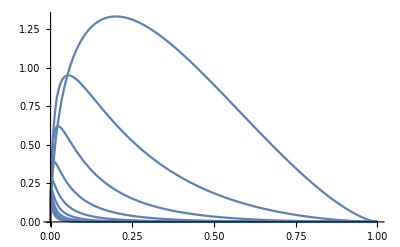

```mathematica
evals=Table[model/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}];
functor[i_]:=Module[{},
Function[{x},Evaluate[evals[[i]]]]
]
funcs=Table[functor[bounceIndex],{bounceIndex,1,bouncesCount}];
Plot[funcs[[2]][x],{x,0,1}];
Show[Table[Plot[evals[[i]]/.x-> t,{t,0,1},PlotRange->All],{i,1,10}]];
Show[Table[Plot[funcs[[i]][x],{x,0,1},PlotRange->All],{i,1,10}]]
```

Trying to normalize the curves by dividing by the “constraint” term x*(1-x)^1.5

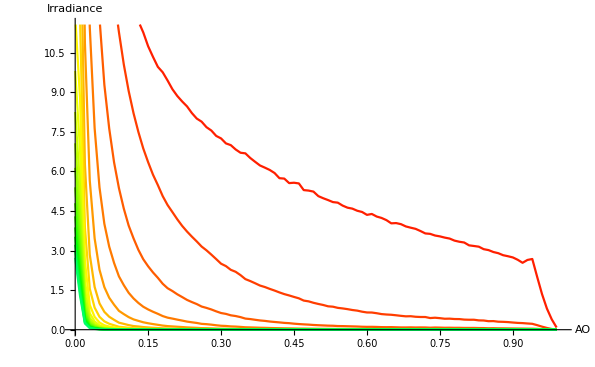

```mathematica
Show[
Table[
ListLinePlot[
Table[ { bounces[[bounceIndex]][[i]][[1]],1/Max[0.01,(i-1)/99*(1-(i-1)/99)^1.5]*bounces[[bounceIndex]][[i]][[2]]},{i,1,tableSize}],PlotRange->{{0,1},{0,10+π/2}},PlotStyle->Hue[bounceIndex/50],AxesLabel->{"AO","Irradiance"}],{bounceIndex,1,bouncesCount}]
]
```

```mathematica
tableBouncesCount=8;
ta3Ddiv=Table[Table[ (bounces[[i]][[j]][[2]])/Max[0.01,(j-1)/99*(1-(j-1)/99)^1.5],{i,1,tableBouncesCount}],{j,1,100}];
ListPlot3D[ta3Ddiv,PlotRange->{0,12},AxesLabel->{"Bounce Index","100*AO","Normalized Irradiance"}]
ta3D=Table[Table[bounces[[i]][[j]][[2]],{i,1,tableBouncesCount}],{j,1,100}];
ListPlot3D[ta3D,PlotRange->{0,π/2},AxesLabel->{"Bounce Index","100*AO","Normalized Irradiance"}]
```

-Graphics3D-

-Graphics3D-

Fourier analysis??

We need to find curves so that the sum of infinite bounces equals π-F0

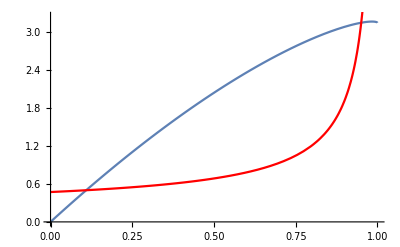

```mathematica
(*E0[x_]=π*x*(1+0.5*(1-x)^0.75);*)
Show[Plot[E0[x],{x,0,1},PlotRange->{0,0.1+π}],Plot[0.1*E0[x]/(x*(1-x)^0.75),{x,0,1},PlotRange->Full,PlotStyle->Red]]
```

Let’s isolate the first bounce curve:

{a→0.0385112,b→3.33644,c→1.85629,d→1.85629}

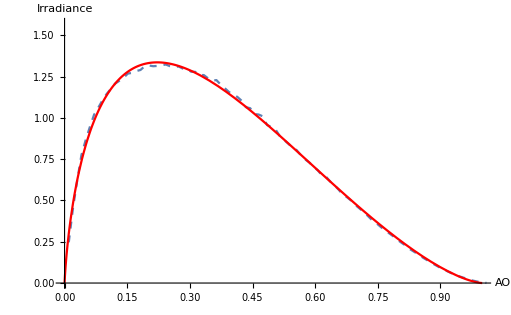

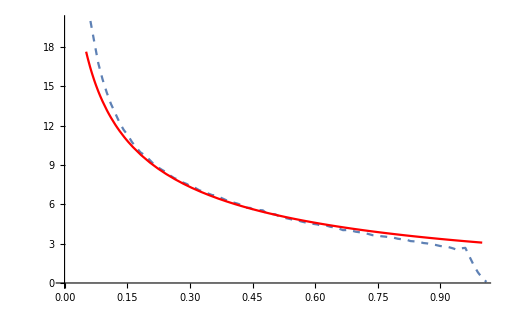

```mathematica
Clear[AO,A0]
coeffsA0=Table[{i/(tableSize-1), ta3D[[i]][[1]]},{i,1,100}];
modelA0=b/a*x*Max[0.0,(1-x)]^1.5*Exp[-b*x^c];
modelA0=b/a*x*Max[0.0,(1-x)]^1.5*Exp[-b*x^0.25];
fitA0=FindFit[coeffsA0,{modelA0,a>0,b>0,c>0,d>0},{{a,1},{b,1},{c,1},{d,1}},x]
A0=Function[{x},Evaluate[modelA0/.fitA0]];
Show[
ListLinePlot[coeffsA0,PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed,AxesLabel->{"AO","Irradiance"}]
(*,Plot[A0[x],{x,0,1},PlotStyle->Red]*)
,Plot[86.635502983679205*x*(1-x)^1.5 ⅇ^(-3.3364392003423804* x^0.25),{x,0,1},PlotStyle->Red]
]
Show[
ListLinePlot[Table[{i/(tableSize-1), ta3Ddiv[[i]][[1]]},{i,1,100}],PlotRange->{{0,1},{0,20}},PlotStyle->Dashed],
Plot[(modelA0/.fitA0)/(x*(1-x)^1.5),{x,0,1},PlotStyle->Red]
]
```

```mathematica
(*coeffsA1=Table[{i/(tableSize-1), ta3D[[i]][[2]]},{i,1,100}];
modelA1=a*x*Max[0.0,(1-x)]^1.5*Exp[-b*x^c];
fitA1=FindFit[coeffsA1,{modelA1,a>0,b>0,c>0,d>0},{{a,1},{b,1},{c,1},{d,1}},x]
Show[
ListLinePlot[coeffsA1,PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[modelA1/.fitA1,{x,0,1},PlotStyle->Red]
]*)
```

#### Rotating the Graph

Now, let’s switch axes and see how the exponential decay is behaving, depending on bounce index:

```mathematica
Clear[ta3DDivOrtho]
ta3DOrtho=Table[Table[bounces[[bounceIndex]][[sampleIndex]][[2]],{bounceIndex,1,bouncesCount}],{sampleIndex,1,samplesCount}];
ta3DOrthoDiv=Table[Table[(bounces[[bounceIndex]][[sampleIndex]][[2]])/Max[0.01,(sampleIndex-1)/(samplesCount-1)*(1-(sampleIndex-1)/(samplesCount-1))^1.5],{bounceIndex,1,bouncesCount}],{sampleIndex,1,samplesCount}];
Manipulate[ListLinePlot[ta3DOrthoDiv[[sampleIndex]],PlotRange->{{0,8},{0,20}}],{{sampleIndex,10},1,samplesCount,1}]
```

```mathematica
ListPlot3D[ta3DOrthoDiv,PlotRange->{{0,bouncesCount},{0,samplesCount},{0,20}},AxesLabel->{"Bounce Index","100*AO","Normalized Irradiance"}]
```

-Graphics3D-

{b→0.485883}

Function[{x},13.2698 ⅇ^(-0.485883 (-1+x))]

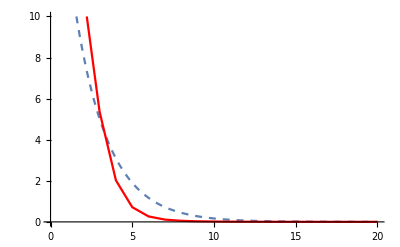

```mathematica
α=0.1;
sampleIndex=Round[α*samplesCount];
amplitude0=A0[α]/(α*(1-α)^1.5);
modelDecay=amplitude0*Exp[-b*(x-1)];
(*fitDecay={x->AO,a-> amplitude0, FindFit[ta3DDivOrtho[[sampleIndex]],modelDecay,{b},{x}][[1]]};*)
fitDecay=FindFit[ta3DOrthoDiv[[sampleIndex]],modelDecay,{b},{x}]
funcDecay=Function[{x},Evaluate[modelDecay/.fitDecay]]
Show[Plot[funcDecay[x],{x,1,bouncesCount},PlotRange->{0,10},PlotStyle->Dashed],ListLinePlot[ta3DOrthoDiv[[sampleIndex]],PlotRange->{0,10},PlotStyle->Red]]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

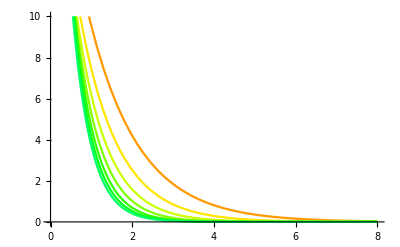

```mathematica
fitter[sampleIndex_]:=Module[{},
α=(sampleIndex-1)/(samplesCount-1);
amplitude0=A0[α]/Max[0.001,α*(1-α)^1.5]; (* Normalized amplitude for initial bounce *)
modelDecay=amplitude0*Exp[-b*(x-1)];
fitDecay=FindFit[ta3DOrthoDiv[[sampleIndex]],modelDecay,{b},{x}];
Function[{x},Evaluate[modelDecay/.fitDecay]]
]
funcsDecay=Table[fitter[sampleIndex],{sampleIndex,1,samplesCount}];
Show[Table[Plot[funcsDecay[[i]][x],{x,0,8},PlotRange->{0,10},PlotStyle->Hue[i/200]],{i,20,samplesCount-20,10}]]
```

```mathematica
Manipulate[Show[
ListLinePlot[ta3DOrthoDiv[[sampleIndex]],PlotRange->{{0,8},{0,10}},PlotStyle->Dashed],
Plot[funcsDecay[[sampleIndex]][x],{x,0,8},PlotRange->Full,PlotStyle->Red]
],{{sampleIndex,10},1,samplesCount,1}]
```

Now let’s examine the decay factors that were fitted:

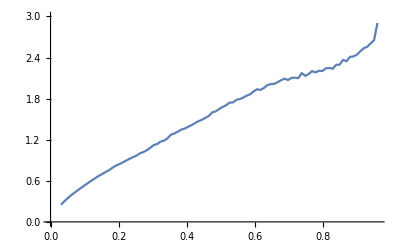

```mathematica
fitter[sampleIndex_]:=Module[{},
α=(sampleIndex-1)/(samplesCount-1);
amplitude0=A0[α]/Max[0.001,α*(1-α)^1.5]; (* Normalized amplitude for initial bounce *)
modelDecay=amplitude0*Exp[-b*(x-1)];
fitDecay=FindFit[ta3DOrthoDiv[[sampleIndex]],modelDecay,{b},{x}];
b/.fitDecay
]
decayCoeffs=Table[{(sampleIndex-1)/(samplesCount-1), fitter[sampleIndex]},{sampleIndex,4,samplesCount-4}];
ListLinePlot[decayCoeffs,PlotRange->{0,3}]
```

Interestingly enough, they seem to obey a linear fit:

{a→0.351265,b→2.44629}

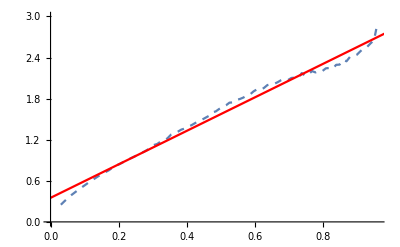

```mathematica
modelDecay=a+x*b;
fitDecay=FindFit[decayCoeffs,modelDecay,{a,b},{x}]
funcDecay=Function[{x},Evaluate[modelDecay/.fitDecay]];
Show[ListLinePlot[decayCoeffs,PlotRange->{0,3},PlotStyle->Dashed],Plot[funcDecay[x],{x,0,1},PlotStyle->Red]]
```

So let’s wrap it up and write the final function. We saw that the initial irradiance value for bounce 1 as a function of AO (α) is given by:
	A(α)=92.9914*α*(1-α)^1.5 ⅇ^(-3.40212*x^0.24245)

Then we modeled exponential decay along the “bounces” axis as:
	B(α,β)=ⅇ^(-(0.349758+α*2.45177) * β)

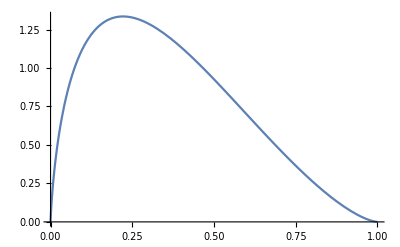

-Graphics3D-

```mathematica
Clear[α,β]
A[α_]:=92.9914*α*(1-α)^1.5 Exp[-3.40212*α^0.24245];
B[α_,β_]=ⅇ^(-(0.3497576886969898+α * 2.4517719576686847) * (β-1));
Plot[A[x],{x,0,1}]
Plot3D[B[x,y],{y,1,10},{x,0,1},PlotRange->{0,1}]
```

Putting it all together, we can obtain the final graph:

```mathematica
(*ta3D=Table[Table[bounces[[i]][[j]][[2]],{i,1,tableBouncesCount}],{j,1,100}];*)
ta3DFit=Table[Table[A[(a-1)/(samplesCount-1)]*B[(a-1)/(samplesCount-1),b],{b,1,tableBouncesCount}],{a,1,samplesCount}];
Show[
ListPlot3D[ta3D,PlotRange->{0,π/2},AxesLabel->{"Bounce Index","100*AO","Normalized Irradiance"}],
ListPlot3D[ta3DFit,PlotRange->Full,PlotStyle->Red]
]
```

-Graphics3D-

One can obviously use the initial bounce coefficient and the bounce decay factor applied repeatedly:
	B_0(α)=ⅇ^(-0.349758-2.45177 * α)

Using exp2(), also equal to:
	B_(0_log2)(α)=2^(-0.504594-3.537156 * α)

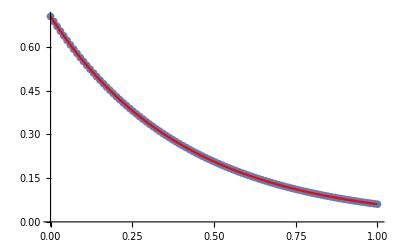

-Graphics3D-

-Graphics3D-

```mathematica
decayCoeffs=Table[{(a-1)/(samplesCount-1),B[(a-1)/(samplesCount-1),2]},{a,1,samplesCount}];
decayCoeffs=Table[{(a-1)/(samplesCount-1),2^(-0.50459413211124206343139253657786-((a-1)/(samplesCount-1))*3.53715642040033381326284253514)},{a,1,samplesCount}];
Show[ListPlot[decayCoeffs,PlotRange->Full],Plot[ⅇ^(-0.3497576886969898-2.4517719576686847 * α),{α,0,1},PlotRange->Full,PlotStyle->Red]]
ta3DFit2=Table[Table[A[(a-1)/(samplesCount-1)]*(decayCoeffs[[a]][[2]])^(b-1),{b,1,tableBouncesCount}],{a,1,samplesCount}];
Show[
ListPlot3D[ta3D,PlotRange->{0,π/2},AxesLabel->{"Bounce Index","100*AO","Normalized Irradiance"}],
ListPlot3D[ta3DFit2,PlotRange->Full,PlotStyle->Red]
]
ListPlot3D[Abs[ta3DFit2-ta3D],PlotRange->Full,PlotStyle->Red]
```

Let’s try and redo the summation using our fitted functions:

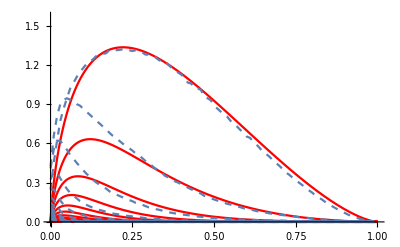

```mathematica
Clear[α,a,b,c,x]
B0[x_]=ⅇ^(-0.3497576886969898- 2.4517719576686847*x);
Show[
Table[Plot[ A[α]*B0[α]^(b-1),{α,0,1},PlotRange->{0,π/2},PlotStyle->Red]
,{b,1,bouncesCount}],
Table[ListLinePlot[bounces[[b]],PlotRange->Full,PlotStyle->Dashed],{b,1,bouncesCount}]
]
```

We’re missing the fit quite a bit!
If we start with a nice fit for the first bounce, can we find the successive bounce values using what we know of the function?

We saw that summing an infinity of bounces yields π : 

	E_0(α) + ρE_1(α)+ ρ^2 E_2(α)+ ρ^3 E_3(α)+(...) =π	for ρ=1
	
Where E_0(α) is the irradiance that is directly perceived, E_1(α) the irradiance perceived after a single bounce, etc. 

Let’s assume, for any AO value α and reflectance ρ=1, that we can rewrite E_2, E_3, etc. as:

	E_2(α)=τ*E_1(α)
	E_3(α)=τ*E_2(α)=τ^2*E_1(α)
	E_4(α)=τ*E_3(α)=τ^3*E_1(α)
	(…)

So:
	E_0(α)+E_1(α)+τ E_1(α)+τ^2 E_1(α)+τ^3 E_1(α)+…=π
	
Finally:
	E_0(α)+E_1(α)  ∑_(b=0)^∞ τ^b=π

We can find the infinite sum involving τ from this expression:

	(π-E_0(α))/(E_1(α))= ∑_(b=0)^∞ τ^b

We know that the τ constant gives decreasing amplitudes at each new bounce, so τ < 1.
Since the sum of a converging geometric series is given by:
	 ∑_(b=0)^∞ τ^b=1/(1-τ)

Solving for τ :
	(π-E_0(α))/(E_1(α))=1/(1-τ)
	(E_1(α))/(π-E_0(α))=1-τ
	τ=1-(E_1(α))/(π-E_0(α))
	
And so, finally let’s use τ for ρ=1 and apply it to retrieve the general expression:
	E(α,ρ) = E_0(α)+ρ [E_1(α)+ρτ E_1(α)+(ρτ)^2 E_1(α)+(ρτ)^3 E_1(α)+… ]=E_0(α)+ρ/(1-ρτ)E_1(α)

```mathematica
Clear[tau,ρ]
F0[α_]=α*(1+(1-α)^0.75/2)
F1[α_]:=27.576937094210384876503293303541*α*(1-α)^1.5 Exp[-3.3364392003423804*√(√α)];
tau[α_]:=1-F1[α]/Max[0.001,1-F0[α]];
tau[0.1];
Manipulate[Plot[tau[α],{α,0,1},PlotRange->Full],{ρ,0.001,1}];
Manipulate[
finalTable1=Table[{(i-1)/(tableSize-1),E0[(i-1)/(tableSize-1)]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}]},{i,1,tableSize}];
Show[
Plot[π*(F0[α]+ F1[α]*ρ/(1-ρ*tau[α])),{α,0,1},PlotRange->{0,0.1+π},PlotStyle->Red],
ListLinePlot[finalTable1,PlotRange->{0,0.1+π},PlotStyle->Dashed]
],{{ρ,0.4},0.001,1}]
```

(1+1/2 (1-α)^0.75) α

Part::partw: Part 21 of {{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 18 », {« 1 »}} does not exist.

Part::partd: Part specification 21 ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 21 of {{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 18 », {« 1 »}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification 21. ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 21 of {{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 18 », {« 1 »}} does not exist.

Part::partd: Part specification 21 ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 21 of {{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 18 », {« 1 »}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification 21. ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 21 of {{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 18 », {« 1 »}} does not exist.

Part::partd: Part specification 21 ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 21 of {{{0, 0.246685}, {1/100, 0.454639}, {1/50, 0.621233}, {3/100, 0.774937}, {1/25, 0.865385}, {1/20, 0.945319}, {3/50, 1.01961}, {7/100, 1.06215}, {2/25, 1.10749}, {9/100, 1.14568}, {1/10, 1.17656}, {11/100, 1.20788}, {3/25, 1.22484}, « 25 », {19/50, 1.15617}, {39/100, 1.14221}, {2/5, 1.12608}, {41/100, 1.10332}, {21/50, 1.06482}, {43/100, 1.05874}, {11/25, 1.02301}, {9/20, 1.02041}, {23/50, 1.00946}, {47/100, 0.956672}, {12/25, 0.945638}, {49/100, 0.930258}, « 50 »}, « 18 », {« 1 »}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification 21. ⟦ 2 ⟧ is longer than depth of object.

Table::iterb: Iterator {i, 1, tableSize} does not have appropriate bounds.

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

NSum::nslim: Limit of summation bouncesCount is not a number.

Table::iterb: Iterator {i, 1., tableSize} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Table::itform: Argument VectorQ[{i, 1, tableSize}] at position 2 does not have the correct form for an iterator.

ListLinePlot::lpn: Table[{i - 1./-1. + tableSize, E0[i - 1./-1. + tableSize] + NSum[FE`ρ$$5^j\ Part[« 2 »] ⟦ i ⟧ ⟦ 2 ⟧, {j, 1., bouncesCount}, WorkingPrecision → 26., AccuracyGoal → ∞, PrecisionGoal → 16.]}, {i, 1., tableSize}] is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

NSum::nslim: Limit of summation bouncesCount is not a number.

Table::itform: Argument VectorQ[{i, 1, tableSize}] at position 2 does not have the correct form for an iterator.

General::stop: Further output of Table :: itform will be suppressed during this calculation.

ListLinePlot::lpn: Table[{i - 1./-1. + tableSize, E0[i - 1./-1. + tableSize] + NSum[FE`ρ$$5^j\ Part[« 2 »] ⟦ i ⟧ ⟦ 2 ⟧, {j, 1., bouncesCount}, WorkingPrecision → 26., AccuracyGoal → ∞, PrecisionGoal → 16.]}, {i, 1., tableSize}] is not a list of numbers or pairs of numbers.

NSum::nslim: Limit of summation bouncesCount is not a number.

General::stop: Further output of NSum :: nslim will be suppressed during this calculation.

ListLinePlot::lpn: Table[{i - 1./-1. + tableSize, E0[i - 1./-1. + tableSize] + NSum[FE`ρ$$5^j\ Part[« 2 »] ⟦ i ⟧ ⟦ 2 ⟧, {j, 1., bouncesCount}, WorkingPrecision → 26., AccuracyGoal → ∞, PrecisionGoal → 16.]}, {i, 1., tableSize}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

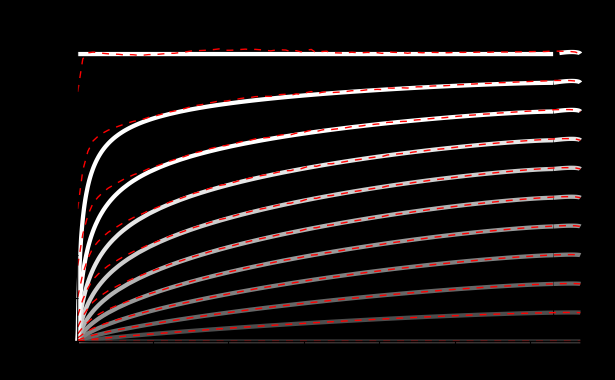

```mathematica
Clear[E1]
(*E1[α_]:=86.635502983679205*α*(1-α)^1.5 Exp[-3.3364392003423804*√(√α)];*)
Show[
Table[Plot[ρ/π * π*(F0[α]+ F1[α]*ρ/(1-ρ*tau[α])),{α,0,1},PlotRange->{0,1.1},PlotStyle->{GrayLevel[ρ+0.2],Thickness-> 0.005},Background->Black,AxesLabel->{"AO","Outgoing Radiance"},LabelStyle->White],{ρ,0,1,0.1}],
Table[
ListLinePlot[Table[{(i-1)/(tableSize-1),ρ/π * (E0[(i-1)/(tableSize-1)]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}])},{i,1,tableSize}],PlotRange->{0,1.1},PlotStyle->{Dashed,Thin,Red},Background->Black]
,{ρ,0,1,0.1}]
]
```

## Runtime Use of the AO value

For runtime use, we (incorrectly!) simplify the integral for directly-perceived illuminance ∫L(x,ω_i) V(x,ω_i) cosθ sinθⅆθ ≈[∫L(x,ω_i) cosθ sinθⅆθ]  [∫V(x,ω_i)  sinθⅆθ] = E(x,n) . AO
The integration of the constant visibility term for a flat, unoccluded surface equals 2π, so we need to apply a 1/(2π)factor to obtain the classical AO term we find in a AO texture.
So let’s decide that an AO map’s value should be multiplied by the irradiance perceived by the surface to obtain a [0,π] value that we later scale by the surface’s albedo ρ/π to finally obtain the reflected radiance in the range [0,1] in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π AO E(x)

Symbolic integration of the cosine-weighted constant luminance L(x,ω_i)=1 function ∫L(x,ω_i)cosθ sinθⅆθ=∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
2π * Integrate[Sin[θ],{θ,0,π/2}]
```

π

2 π